### Start choosing the example:

```mathematica
t=1;
```

```mathematica
(*beta=1;A=1;
(*DataIn=*){{1,1}},
(*FinalCosts=*){{1,2}},
(*SwitchingCostsData=*){}},*)
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];//Timing
v0=MFGEquations["criticalreduced1"][[2]]
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Done.

{0.095839,Null}

<|j224→80,u276→15,j214→80,j215→80,j216→80,j217→80,j218→80,j219→80,j220→80,j221→80,j222→80,j223→80,j225→0,j226→0,j227→0,j228→0,j229→0,j230→0,j231→0,j232→0,j233→0,j234→0,j235→0,jt236→0,jt237→80,jt238→80,jt239→0,jt240→80,jt241→0,jt242→80,jt243→0,jt244→80,jt245→0,jt246→80,jt247→0,jt248→80,jt249→0,jt250→80,jt251→0,jt252→80,jt253→0,jt254→80,jt255→0,u265→15,u267→-80+735,u268→-80+655,u269→-80+575,u270→-80+495,u271→-80+415,u272→-80+335,u273→-80+255,u274→-80+175,u275→-80+95,u277→735,u256→735,u257→655,u258→575,u259→495,u260→415,u261→335,u262→255,u263→175,u264→95,u266→735|>

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort//Values
MFGEquations["criticalreduced2"][[2]]//KeySort//Values
```

{80,80,80,80,80,80,80,80,80,80,80,0,0,0,0,0,0,0,0,0,0,0,0,80,80,0,80,0,80,0,80,0,80,0,80,0,80,0,80,0,80,0,735,655,575,495,415,335,255,175,95,15,735,655,575,495,415,335,255,175,95,15,15,735}

{80,80,80,80,80,80,80,80,80,80,80,0,0,0,0,0,0,0,0,0,0,0,0,80,80,0,80,0,80,0,80,0,80,0,80,0,80,0,80,0,80,0,735,655,575,495,415,335,255,175,95,15,735,655,575,495,415,335,255,175,95,15,15,735}

```mathematica
MFGEquations["reduced1"][[2]]//KeySort//Values
MFGEquations["reduced2"][[2]]//KeySort//Values
```

{80,80,80,80,80,80,80,80,80,80,80,0,0,0,0,0,0,0,0,0,0,0,0,80,80,0,80,0,80,0,80,0,80,0,80,0,80,0,80,0,80,0,15,u256,u257,u258,u259,u260,u261,u262,u263,u264,15,15,u256}

{80,80,80,80,80,80,80,80,80,80,80,0,0,0,0,0,0,0,0,0,0,0,0,80,80,0,80,0,80,0,80,0,80,0,80,0,80,0,80,0,80,0,15,u256,u257,u258,u259,u260,u261,u262,u263,u264,15,15,u256}

#### Non-linear case with alpha != 1

```mathematica
Parameters["alpha"]=2;
Parameters
```

<|alpha→2,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$2348[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$2348[x$]-g$2348[m$]]|>

```mathematica
sol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],1, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

<|j224→80.,u276→15,j214→80.,j215→80.,j216→80.,j217→80.,j218→80.,j219→80.,j220→80.,j221→80.,j222→80.,j223→80.,j225→0.,j226→0.,j227→0.,j228→0.,j229→0.,j230→0.,j231→0.,j232→0.,j233→0.,j234→0.,j235→0.,jt236→0.,jt237→80.,jt238→80.,jt239→0.,jt240→80.,jt241→0.,jt242→80.,jt243→0.,jt244→80.,jt245→0.,jt246→80.,jt247→0.,jt248→80.,jt249→0.,jt250→80.,jt251→0.,jt252→80.,jt253→0.,jt254→80.,jt255→0.,u265→15,u277→14.8875,u266→14.8875,u267→0.0125039+1. 14.8875,u268→0.0125039+1. 14.9,u269→0.0125039+1. 14.9125,u270→0.0125039+1. 14.925,u271→0.0125039+1. 14.9375,u272→0.0125039+1. 14.95,u273→0.0125039+1. 14.9625,u274→0.0125039+1. 14.975,u275→0.0125039+1. 14.9875,u256→14.8875,u257→14.9,u258→14.9125,u259→14.925,u260→14.9375,u261→14.95,u262→14.9625,u263→14.975,u264→14.9875|>

Note that 5 iterations work for the X2 solver tools:

```mathematica
sol2 = FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],3, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]
<10^(-6)&)]
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.sol2]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j214-j225-u256+u267==80.0125&&j215-j226-u257+u268==80.0125&&j216-j227-u258+u269==80.0125&&j217-j228-u259+u270==80.0125&&j218-j229-u260+u271==80.0125&&j219-j230-u261+u272==80.0125&&j220-j231-u262+u273==80.0125&&j221-j232-u263+u274==80.0125&&j222-j233-u264+u275==80.0125

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j214-j225-u256+u267==80.0125&&j215-j226-u257+u268==80.0125&&j216-j227-u258+u269==80.0125&&j217-j228-u259+u270==80.0125&&j218-j229-u260+u271==80.0125&&j219-j230-u261+u272==80.0125&&j220-j231-u262+u273==80.0125&&j221-j232-u263+u274==80.0125&&j222-j233-u264+u275==80.0125

<|j224→80.,u276→15,j214→80.,j215→80.,j216→80.,j217→80.,j218→80.,j219→80.,j220→80.,j221→80.,j222→80.,j223→80.,j225→0.,j226→0.,j227→0.,j228→0.,j229→0.,j230→0.,j231→0.,j232→0.,j233→0.,j234→0.,j235→0.,jt236→0.,jt237→80.,jt238→80.,jt239→0.,jt240→80.,jt241→0.,jt242→80.,jt243→0.,jt244→80.,jt245→0.,jt246→80.,jt247→0.,jt248→80.,jt249→0.,jt250→80.,jt251→0.,jt252→80.,jt253→0.,jt254→80.,jt255→0.,u265→15,u267→0.0125039+1. 14.8875,u268→0.0125039+1. 14.9,u269→0.0125039+1. 14.9125,u270→0.0125039+1. 14.925,u271→0.0125039+1. 14.9375,u272→0.0125039+1. 14.95,u273→0.0125039+1. 14.9625,u274→0.0125039+1. 14.975,u275→0.0125039+1. 14.9875,u277→14.8875,u256→14.8875,u257→14.9,u258→14.9125,u259→14.925,u260→14.9375,u261→14.95,u262→14.9625,u263→14.975,u264→14.9875,u266→14.8875|>

4.19456×10^-15

But if we try one more iteration, the next system is False. Now we have to create a way to deal with this.

```mathematica
sol26It=FixedPoint[FixedSolverStepX2[MFGEquations], 
MFGEquations["criticalreduced2"][[2]],8, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#2]
<10^(-6)&)]
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.%]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j214-j225-u256+u267==80.0125&&j215-j226-u257+u268==80.0125&&j216-j227-u258+u269==80.0125&&j217-j228-u259+u270==80.0125&&j218-j229-u260+u271==80.0125&&j219-j230-u261+u272==80.0125&&j220-j231-u262+u273==80.0125&&j221-j232-u263+u274==80.0125&&j222-j233-u264+u275==80.0125

<|j224→80.,u276→15,j214→80.,j215→80.,j216→80.,j217→80.,j218→80.,j219→80.,j220→80.,j221→80.,j222→80.,j223→80.,j225→0.,j226→0.,j227→0.,j228→0.,j229→0.,j230→0.,j231→0.,j232→0.,j233→0.,j234→0.,j235→0.,jt236→0.,jt237→80.,jt238→80.,jt239→0.,jt240→80.,jt241→0.,jt242→80.,jt243→0.,jt244→80.,jt245→0.,jt246→80.,jt247→0.,jt248→80.,jt249→0.,jt250→80.,jt251→0.,jt252→80.,jt253→0.,jt254→80.,jt255→0.,u265→15,u267→0.0125039+1. 14.8875,u268→0.0125039+1. 14.9,u269→0.0125039+1. 14.9125,u270→0.0125039+1. 14.925,u271→0.0125039+1. 14.9375,u272→0.0125039+1. 14.95,u273→0.0125039+1. 14.9625,u274→0.0125039+1. 14.975,u275→0.0125039+1. 14.9875,u277→14.8875,u256→14.8875,u257→14.9,u258→14.9125,u259→14.925,u260→14.9375,u261→14.95,u262→14.9625,u263→14.975,u264→14.9875,u266→14.8875|>

4.19456×10^-15

```mathematica
sol36It=Catch @ FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#2]
<10^(-6)&)]
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.%]
```

FixedX3: next step: j214-j225-u256+u267==80.0125&&j215-j226-u257+u268==80.0125&&j216-j227-u258+u269==80.0125&&j217-j228-u259+u270==80.0125&&j218-j229-u260+u271==80.0125&&j219-j230-u261+u272==80.0125&&j220-j231-u262+u273==80.0125&&j221-j232-u263+u274==80.0125&&j222-j233-u264+u275==80.0125

<|j224→80.,u276→15,j214→80.,j215→80.,j216→80.,j217→80.,j218→80.,j219→80.,j220→80.,j221→80.,j222→80.,j223→80.,j225→0.,j226→0.,j227→0.,j228→0.,j229→0.,j230→0.,j231→0.,j232→0.,j233→0.,j234→0.,j235→0.,jt236→0.,jt237→80.,jt238→80.,jt239→0.,jt240→80.,jt241→0.,jt242→80.,jt243→0.,jt244→80.,jt245→0.,jt246→80.,jt247→0.,jt248→80.,jt249→0.,jt250→80.,jt251→0.,jt252→80.,jt253→0.,jt254→80.,jt255→0.,u265→15,u267→0.0125039+1. 14.8875,u268→0.0125039+1. 14.9,u269→0.0125039+1. 14.9125,u270→0.0125039+1. 14.925,u271→0.0125039+1. 14.9375,u272→0.0125039+1. 14.95,u273→0.0125039+1. 14.9625,u274→0.0125039+1. 14.975,u275→0.0125039+1. 14.9875,u277→14.8875,u256→14.8875,u257→14.9,u258→14.9125,u259→14.925,u260→14.9375,u261→14.95,u262→14.9625,u263→14.975,u264→14.9875,u266→14.8875|>

4.19456×10^-15

#### Non-linear case with alpha = 1

```mathematica
Parameters["alpha"]=1;
Parameters
```

<|alpha→1,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$2348[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$2348[x$]-g$2348[m$]]|>

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]//KeySort//Values
```

{80,80,80,80,80,80,80,80,80,80,80,0,0,0,0,0,0,0,0,0,0,0,0,80,80,0,80,0,80,0,80,0,80,0,80,0,80,0,80,0,80,0,735,655,575,495,415,335,255,175,95,15,735,655,575,495,415,335,255,175,95,15,15,735}

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]//KeySort//Values
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j214-j225-u256+u267==0&&j215-j226-u257+u268==0&&j216-j227-u258+u269==0&&j217-j228-u259+u270==0&&j218-j229-u260+u271==0&&j219-j230-u261+u272==0&&j220-j231-u262+u273==0&&j221-j232-u263+u274==0&&j222-j233-u264+u275==0

{80,80,80,80,80,80,80,80,80,80,80,0,0,0,0,0,0,0,0,0,0,0,0,80,80,0,80,0,80,0,80,0,80,0,80,0,80,0,80,0,80,0,735,655,575,495,415,335,255,175,95,15,735,655,575,495,415,335,255,175,95,15,15,735}

```mathematica
nsol3=FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced2"][[2]],9, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-9)&)]//KeySort//Values
```

FixedX3: next step: j214-j225-u256+u267==0&&j215-j226-u257+u268==0&&j216-j227-u258+u269==0&&j217-j228-u259+u270==0&&j218-j229-u260+u271==0&&j219-j230-u261+u272==0&&j220-j231-u262+u273==0&&j221-j232-u263+u274==0&&j222-j233-u264+u275==0

{80,80,80,80,80,80,80,80,80,80,80,0,0,0,0,0,0,0,0,0,0,0,0,80,80,0,80,0,80,0,80,0,80,0,80,0,80,0,80,0,80,0,735,655,575,495,415,335,255,175,95,15,735,655,575,495,415,335,255,175,95,15,15,735}

### What is this plot for?

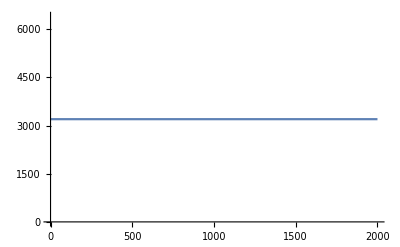
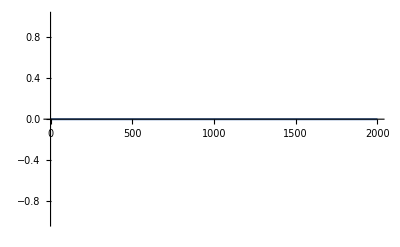
<|{2,1->2}→-Graphics-,{ex81,2->ex81}→-Graphics-,{1,en80->1}→-Graphics-,{1,1->2}→-Graphics-,{2,2->ex81}→-Graphics-,{en80,en80->1}→-Graphics-|>

```mathematica
Function[a,ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-a/(m^(1-alpha)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will always retrieve the most up - to - date values.